```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;Clear[κ];rep={a1->Subscript[a, 1],a2->Subscript[a, 2],a3->Subscript[a, 3],κi->Subscript[κ, i],κr->Subscript[κ, r],kx->Subscript[k, x], ky->Subscript[k, y], kz->Subscript[k, z], vz->Subscript[v, z], vp->Subscript[v, p],en->e,b1->Subscript[b, 1],b2->Subscript[b, 2],b3->Subscript[b, 3]};
ass=Assumptions->{a1,b1,,ky,kz,t,κi,κr,μ}∈ Reals &&  k>0 && kp>0 && ek>0 && v>0 && μ>0;
sx=({{0, 1}, {1, 0}});sy=({{0, -ⅈ}, {ⅈ, 0}});sz=({{1, 0}, {0, -1}});
id=({{1, 0}, {0, 1}});
```

## Prel

```mathematica
(* -Graphics- -Graphics-*)
(kx+ⅈ ky)^3(σx-ⅈ σy)/2+(kx-ⅈ ky)^3(σx+ⅈ σy)/2//FullSimplify
```

kx^3 σx-3 kx ky^2 σx+3 kx^2 ky σy-ky^3 σy

```mathematica
Clear[ham,eval,dx,dy,dz,κ,k0];k0=1;
{dx,dy,dz}={ kx^3-3 kx ky^2,3 kx^2 ky-ky^3,kz};
ham=dx sx+dy sy+dz sz;
dx sigx+dy sigy+dz sigz/.{kx->-ⅈ Dx}//Expand
FullSimplify[Eigensystem[ham]]
```

ⅈ Dx^3 sigx+3 ⅈ Dx ky^2 sigx-3 Dx^2 ky sigy-ky^3 sigy+kz sigz

{{-√((kx^2+ky^2)^3+kz^2),√((kx^2+ky^2)^3+kz^2)},{{(kz-√((kx^2+ky^2)^3+kz^2))/(kx+ⅈ ky)^3,1},{(kz+√((kx^2+ky^2)^3+kz^2))/(kx+ⅈ ky)^3,1}}}

## More tries->do not work

```mathematica
Clear[eq0,prod,solu,κ,κr,κi,a1,b1,a];
κ=κr+ⅈ κi;
ψ={1,a1+ⅈ b1};
ψdag={1,a1-ⅈ b1};
prod=FullSimplify[ (3 ky^2+(κr+ⅈ κi)^2+(κr-ⅈ κi)^2-(κr^2+κi^2))ψdag.(sz.ψ)+6ky κi ψdag.(sy.ψ),ass]/2;
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1]
t=(*0.5//N*)0;
a1=a Cos[t];b1=a Sin[t];
eq0[[1]]//FullSimplify
eq=FullSimplify[ⅈ (-κ)^3sz.ψ+ 3ⅈ ky^2(-κ)sz.ψ -3ky sy.ψ(-κ)^2-ky^3 sy.ψ+kz sx.ψ-en id.ψ ]/.{κi^2->κisq}//FullSimplify;
eqn=(Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1])(*/.{κr^3->krsq κr,κr^2->krsq}*);
Clear[a1,b1,κi,t];
FullSimplify[Solve[ eqn[[1]]==0  && eqn[[2]]==0 && eqn[[3]]==0  && eqn[[4]]==0 && κr≠0,{en,κr,κi, a}],ass]
Clear[t];
```

{1/2 (-3 (-1+a1^2+b1^2) ky^2+12 b1 ky κi+(-1+a1^2+b1^2) (3 κi^2-κr^2)),0}

-1/2 (-1+a^2) (3 ky^2-3 κi^2+κr^2)

{{en→-kz,κr→-ky,κi→0,a→-1},{en→kz,κr→ky,κi→0,a→1},{en→((12 ky^3-√3 kz) √(-((512 ky^6-27 kz^2) (48 ky^6+8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2),κr→-ky,κi→-(2 ky)/(√3),a→-(336 ky^6+28 √3 ky^3 kz+√3 √(-((512 ky^6-27 kz^2) (48 ky^6+8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2)},{en→((-12 ky^3+√3 kz) √(-((512 ky^6-27 kz^2) (48 ky^6+8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2),κr→-ky,κi→-(2 ky)/(√3),a→(-336 ky^6-28 √3 ky^3 kz+√3 √(-((512 ky^6-27 kz^2) (48 ky^6+8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2)},{en→-((12 ky^3+√3 kz) √(-((512 ky^6-27 kz^2) (48 ky^6-8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2),κr→ky,κi→-(2 ky)/(√3),a→(336 ky^6-28 √3 ky^3 kz-√3 √(-((512 ky^6-27 kz^2) (48 ky^6-8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2)},{en→((12 ky^3+√3 kz) √(-((512 ky^6-27 kz^2) (48 ky^6-8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2),κr→ky,κi→-(2 ky)/(√3),a→(336 ky^6-28 √3 ky^3 kz+√3 √(-((512 ky^6-27 kz^2) (48 ky^6-8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2)},{en→-((12 ky^3+√3 kz) √(-((512 ky^6-27 kz^2) (48 ky^6-8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2),κr→-ky,κi→(2 ky)/(√3),a→(-336 ky^6+28 √3 ky^3 kz-√3 √(-((512 ky^6-27 kz^2) (48 ky^6-8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2)},{en→((12 ky^3+√3 kz) √(-((512 ky^6-27 kz^2) (48 ky^6-8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2),κr→-ky,κi→(2 ky)/(√3),a→(-336 ky^6+28 √3 ky^3 kz+√3 √(-((512 ky^6-27 kz^2) (48 ky^6-8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2)},{en→((12 ky^3-√3 kz) √(-((512 ky^6-27 kz^2) (48 ky^6+8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2),κr→ky,κi→(2 ky)/(√3),a→(336 ky^6+28 √3 ky^3 kz-√3 √(-((512 ky^6-27 kz^2) (48 ky^6+8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2)},{en→((-12 ky^3+√3 kz) √(-((512 ky^6-27 kz^2) (48 ky^6+8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2),κr→ky,κi→(2 ky)/(√3),a→(336 ky^6+28 √3 ky^3 kz+√3 √(-((512 ky^6-27 kz^2) (48 ky^6+8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2)}}

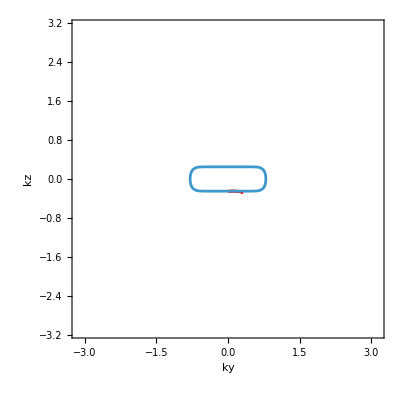

```mathematica
mu=0.25;lim=π;
c1=ContourPlot[((-12 ky^3+√3 kz) √(-((512 ky^6-27 kz^2) (48 ky^6+8 √3 ky^3 kz+kz^2))))/(432 ky^6-9 kz^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},ContourStyle->Red, PlotLegends->Automatic,RegionFunction->Function[{ky,kz,z},ky>0 && -((512 ky^6-27 kz^2) (48 ky^6+8 √3 ky^3 kz+kz^2))>=0]]//Quiet;
c2=c1;

fs=ContourPlot[√((ky^2)^6+(kz)^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},Contours->20,PlotLegends->Automatic];
Show[c1,c2,fs]
Clear[κr,a1];
```

```mathematica
Clear[dat,κrsq];
dat[μ_,pts_]:=Module[{en=μ,kz,t=0,κr,kx,ky,a,del=2π/pts,i,j,dat={},eq,κi,sol,s,len},
(*κr=√(-3 (ky^2-κi^2+2 ky κi Tan[t]));*)
s={a (3 ky^2-3 κi^2+κr^2) Cos[t]+6 a ky κi Sin[t],-en+kz-a κi (κi^2-3 (ky-κr)^2) Cos[t]-a (-3 κi^2+(ky-κr)^2) (ky-κr) Sin[t],a ((-3 κi^2+(ky-κr)^2) (ky-κr) Cos[t]-κi (κi^2-3 (ky-κr)^2) Sin[t]),κi (-κi^2+3 (ky+κr)^2)-a (en+kz) Cos[t],-((ky+κr) (-3 κi^2+(ky+κr)^2))-a (en+kz) Sin[t]};
For[i=0,i<=pts,i++,
ky=-π*1.0+i del;
sol=Simplify[SolveValues[s[[5]]==0 && s[[2]]==0 && s[[3]]==0 && s[[4]]==0,{kx,κi,a}]//Quiet];(*Print[sol];*)
len=Length[sol];
(**)
For[j=1,j<=len,j++,
If[ κr>0,dat=AppendTo[dat,{ky,sol[[j,1]]}]]
]
(**)];dat]
dat[0.5,20]
```

{}

## analytics

```mathematica
g=(3 √3 kz-√(-512 ky^6+27 kz^2))/(64 ky^3)/.rep;
TeXForm[g]
```

\frac{3 \sqrt{3} k_z-\sqrt{27 k_z^2-512 k_y^6}}{64 k_y^3}

```mathematica
Clear[eq0,prod,solu,κ,κr,κi,a1,b1,a];
κ=κr+ⅈ κi;
ψ={1,a1+ⅈ b1};
ψdag={1,a1-ⅈ b1};
prod=FullSimplify[ (3 ky^2+(κr+ⅈ κi)^2+(κr-ⅈ κi)^2-(κr^2+κi^2))ψdag.(sx.ψ)+6ky κi ψdag.(sy.ψ),ass]/2;
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1]
eq=FullSimplify[ⅈ (-κ)^3sx.ψ+ 3ⅈ ky^2(-κ)sx.ψ -3ky sy.ψ(-κ)^2-ky^3 sy.ψ+kz sz.ψ-en id.ψ ]/.{κi^2->κisq}//FullSimplify
eqn=(Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1])
t=(*0.5//N*)0;
a1=a Cos[t];b1=a Sin[t];
eq0[[1]]//FullSimplify
eqn=eqn//FullSimplify
Clear[a1,b1,κi,t];
FullSimplify[Solve[ eqn[[1]]==0  && eqn[[2]]==0 && eqn[[3]]==0  && eqn[[4]]==0 && κr≠0,{en,κr,κi, a}],ass]
Clear[t];
```

{6 b1 ky κi+a1 (3 ky^2-3 κi^2+κr^2),0}

{-en+kz-(a1+ⅈ b1) (ⅈ ky+κi-ⅈ κr)^3,-a1 (en+kz)-ⅈ (b1 (en+kz)+(ky+ⅈ κi+κr)^3)}

{-en+kz-a1 κi (κi^2-3 (ky-κr)^2)-b1 (-3 κi^2+(ky-κr)^2) (ky-κr),-b1 κi (κi^2-3 (ky-κr)^2)+a1 (-3 κi^2+(ky-κr)^2) (ky-κr),-a1 (en+kz)+κi (-κi^2+3 (ky+κr)^2),-b1 (en+kz)-(ky+κr) (-3 κi^2+(ky+κr)^2)}

a (3 ky^2-3 κi^2+κr^2)

{-en+kz-a κi (κi^2-3 (ky-κr)^2),a (-3 κi^2+(ky-κr)^2) (ky-κr),-a (en+kz)+κi (-κi^2+3 (ky+κr)^2),-((ky+κr) (-3 κi^2+(ky+κr)^2))}

```mathematica
{{en->kz,κr->-ky,κi->0,a->0},{en->kz,κr->-ky,κi->0,a->0},{en->1/3 √(-(512 ky^6)/3+9 kz^2),κr->-ky,κi->-(2 ky)/(√3),a->-(-3 √3 kz+√(-512 ky^6+27 kz^2))/(64 ky^3)},{en->1/3 √(-(512 ky^6)/3+9 kz^2),κr->ky,κi->-(2 ky)/(√3),a->(-3 √3 kz+√(-512 ky^6+27 kz^2))/(8 ky^3)},{en->1/3 √(-(512 ky^6)/3+9 kz^2),κr->-ky,κi->(2 ky)/(√3),a->(-3 √3 kz+√(-512 ky^6+27 kz^2))/(64 ky^3)},{en->1/3 √(-(512 ky^6)/3+9 kz^2),κr->ky,κi->(2 ky)/(√3),a->-(-3 √3 kz+√(-512 ky^6+27 kz^2))/(8 ky^3)}}
```

```mathematica
Solve[1/3 √(-(512 ky^6)/3+9 kz^2)==μ,kz]
Solve[kz==μ,kz]
Print["tangents are:"]
{{1,D[(√(512 ky^6+27 μ^2))/(3 √3),ky]},{1,D[-(√(512 ky^6+27 μ^2))/(3 √3),ky]},{1,0}}
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{kz→-(√(512 ky^6+27 μ^2))/(3 √3)},{kz→(√(512 ky^6+27 μ^2))/(3 √3)}}

{{kz→μ}}

tangents are:

{{1,(512 ky^5)/(√3 √(512 ky^6+27 μ^2))},{1,-(512 ky^5)/(√3 √(512 ky^6+27 μ^2))},{1,0}}

```mathematica
{ener,kap}={kz/3 √(-(512 ky^6)/(3 kz^2)+9),pm ky};
soll=FullSimplify[Solve[kap==0 &&  ener==μ,{ky,kz}],ass]
FullSimplify[ √((ky^2)^3+kz^2)/.soll,ass]
{{1,(512 ky^5)/(√3 √(512 ky^6+27 μ^2))},{1,-(512 ky^5)/(√3 √(512 ky^6+27 μ^2))}}/.soll
```

{{ky→0,kz→μ}}

{μ}

{{{1,0},{1,0}}}

## Plot

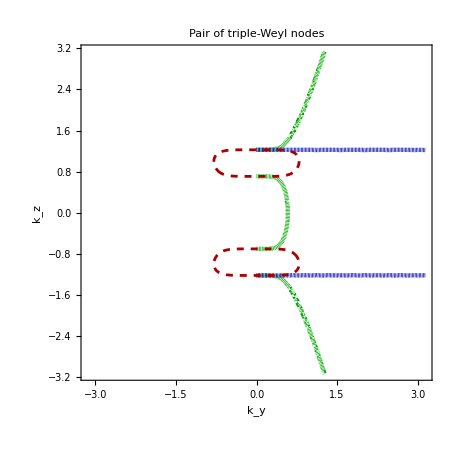

```mathematica
mu=0.5;lim=π;kw=1;th=0.007;
style={Directive[Darker[Cyan],Thickness[th],Opacity[0.75]],(**)Directive[Orange,Thickness[th],Opacity[0.75]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.001]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.001]]};
c1=ContourPlot[1/3 √(9(kz^2-kw^2)^2-(512 ky^6)/3)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style[[4]], RegionFunction->Function[{ky,kz,z},ky>0 && -(512 ky^6)/3+9 (kz^2-kw^2)^2>=0]]//Quiet;
c3=ContourPlot[(kz^2-kw^2)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style[[3]], RegionFunction->Function[{ky,kz,z},ky>0 ]]//Quiet;
fs=ContourPlot[√((ky^2)^3+(kz^2-kw^2)^2)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->{Directive[Darker[Red],Dashed]}];
plt=Show[c1,c3,fs,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->450,PlotLabel->Style[(****)"Pair of triple-Weyl nodes",20,FontFamily->"TexMaths Roman",Brown,Bold]]
SetDirectory[NotebookDirectory[]];
(*Export["tripleWeylarc.pdf",Rasterize[plt],ImageResolution->100];*)
Clear[t,kw];
```

## Alternate

```mathematica
(kx+ⅈ ky)^3/(1(*kz+en*)){(kz+en)/(kx+ⅈ ky)^3,1};
FullSimplify[%/.kx->ⅈ (κr+ⅈ κi)]
Clear[a,b];
{a,b}=ComplexExpand[ReIm[-ⅈ (ky+ⅈ κi+κr)^3]]//FullSimplify
```

{en+kz,-ⅈ (ky+ⅈ κi+κr)^3}

{κi (-κi^2+3 (ky+κr)^2),-((ky+κr) (-3 κi^2+(ky+κr)^2))}

```mathematica
({{en+kz}, {-ⅈ (ky+ⅈ κi+κr)^3}})
```

{{0},{-ⅈ (ky+ⅈ κi+κr)^3}}

```mathematica
Clear[ψ0,ψ0dag,eq0,eq01,eq02];ψ0=({{1}, {-ⅈ (ky+ⅈ κi+κr)^3/(en+kz)}});ψ0dag=({{1, ⅈ (ky-ⅈ κi+κr)^3}}/(en+kz));
FullSimplify[ (3 ky^2+(κr+ⅈ κi)^2+(κr-ⅈ κi)^2-(κr^2+κi^2))ψ0dag.(sx.ψ0)+6ky κi ψ0dag.(sy.ψ0),ass];
eq0=%[[1,1]](en+kz)^2;
{eq01,eq02}=FullSimplify[ComplexExpand[ReIm[eq0]]]
```

{(1+en+kz) κi (3 (ky^2+κi^2)^2-2 (3 ky^2+5 κi^2) κr^2+3 κr^4),(-1+en+kz) (3 ky (ky^2+κi^2)^2+9 (ky^2+κi^2)^2 κr+2 ky (5 ky^2+3 κi^2) κr^2+6 (ky-κi) (ky+κi) κr^3+3 ky κr^4+κr^5)}

```mathematica
Clear[ψ,v,M,hψ,κ,x,en,ky,eq,eqn,κi,sol];
κ=κr+ⅈ κi;
eq1=κr^2+3 ky^2-κi(6 ky tanα-κi);
{dx,dy,dz}={ kx^3-3 kx ky^2,3 kx^2 ky-ky^3,kz};
ψ=({{1}, {-ⅈ (ky+ⅈ κi+κr)^3/(en+kz)}}) ⅇ^(-(κr+ⅈ κi) x);
hψ=dx sxψ+dy syψ+dz szψ/.{kx->-ⅈ Dx}
eq=FullSimplify[ⅈ D[sx.ψ,{x,3}]+ 3ⅈ ky^2 D[sx.ψ,x] -3ky D[sy.ψ,{x,2}]-ky^3 sy.ψ+kz sz.ψ-en id.ψ ]/( ⅇ^(-κ  x))//FullSimplify;
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[(en+kz)eq[[1,1]]]],ass],1]
Clear[κi,κr,κ];
```

(ⅈ Dx^3+3 ⅈ Dx ky^2) sxψ+(-3 Dx^2 ky-ky^3) syψ+kz szψ

{-en^2+kz^2+(ky^2+κi^2-κr^2) ((ky^2+κi^2)^2-2 (ky^2+7 κi^2) κr^2+κr^4),-6 κi (ky^2+κi^2)^2 κr+4 κi (3 ky^2+5 κi^2) κr^3-6 κi κr^5}

```mathematica
μ=1/2;ky=1;
κrsq=κi(6 ky tanα-κi)-3 ky^2;
s={-μ^2+kzsq+(ky^2+κi^2-κrsq) ((ky^2+κi^2)^2-2 (ky^2+7 κi^2) κrsq+κrsq^2),-6 κi (ky^2+κi^2)^2 +4 κi (3 ky^2+5 κi^2) κrsq-6 κi κrsq^2}//FullSimplify;
(*Simplify[SolveValues[s[[1]]==0 && s[[2]]==0,{kzsq,κi}],ass]*)
Clear[tanα,μ,ky];
```

{kzsq+8 (2 ky^2-3 ky tanα κi+κi^2) (4 ky^4-12 ky^3 tanα κi+ky^2 (13+9 tanα^2) κi^2-24 ky tanα κi^3+4 κi^4)-μ^2,-8 κi (12 ky^4-36 ky^3 tanα κi+3 ky^2 (5+9 tanα^2) κi^2-24 ky tanα κi^3+4 κi^4)}

$Aborted

## Numerical

```mathematica
Clear[data,κrsq];
data[tanα_,μ_,pts_]:=Module[{κrsq,ky,kzsq,del=2π/pts,i,j,dat={},eq,κi,κim,sol,s,len},
κrsq=κi(6 ky tanα-κi)-3 ky^2;
s={-μ^2+kzsq+(ky^2+κi^2-κrsq) ((ky^2+κi^2)^2-2 (ky^2+7 κi^2) κrsq+κrsq^2),-6 κi (ky^2+κi^2)^2 +4 κi (3 ky^2+5 κi^2) κrsq-6 κi κrsq^2};
For[i=0,i<=pts,i++,
ky=-π*1.0+i del;
sol=Simplify[SolveValues[s[[1]]==0 && s[[2]]==0 && kzsq>=0,{kzsq,κi},Reals]//Quiet];(*Print[sol];*)
len=Length[sol];
(**)
For[j=1,j<=len,j++,
κim=sol[[j,2]];
If[κim(6 ky tanα-κim)-3 ky^2>0 && κim>=0,
dat=AppendTo[dat,{ky,√sol[[j,1]]}]];
If[κim(6 ky tanα-κim)-3 ky^2>0 && κim>=0,
dat=AppendTo[dat,{ky,-√sol[[j,1]]}]];
If[κim(6 ky tanα-κim)-3 ky^2>0 && κim<0,
dat=AppendTo[dat,{ky,100}]]
]
(**)];dat]
```

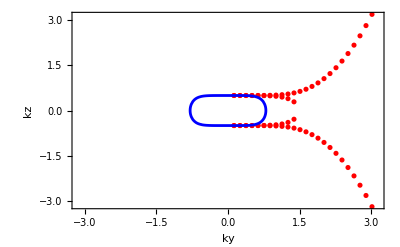

```mathematica
mu=0.5;lim=π;
xdat=data[6,mu,50];
c1=ListPlot[xdat,PlotRange->{-π,π},Frame->True,PlotStyle->Red];
fs=ContourPlot[{√((ky^2)^3+kz^2)==mu},{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},Contours->20,PlotLegends->Automatic,ContourStyle->Blue];
Show[{c1,fs},FrameLabel->{ky,kz}]
Clear[μ]
```

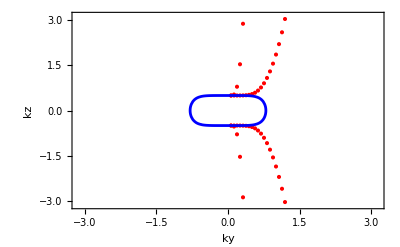

```mathematica
Clear[xdat,c1,fs];
mu=0.5;lim=π;
xdat=data[1,mu,100];
c1=ListPlot[xdat,PlotRange->{-π,π},Frame->True,PlotStyle->Red];
fs=ContourPlot[{√((ky^2)^3+kz^2)==mu},{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},Contours->20,PlotLegends->Automatic,ContourStyle->Blue];
Show[{c1,fs},FrameLabel->{ky,kz}]
Clear[μ]
```

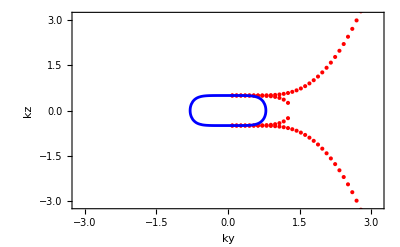

```mathematica
Clear[xdat,c1,fs];
mu=0.5;lim=π;
xdat=data[Tan[π/2-0.2],mu,70];
c1=ListPlot[xdat,PlotRange->{-π,π},Frame->True,PlotStyle->Red];
fs=ContourPlot[{√((ky^2)^3+kz^2)==mu},{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{ky,kz},Contours->20,PlotLegends->Automatic,ContourStyle->Blue];
Show[{c1,fs},FrameLabel->{ky,kz}]
Clear[μ]
```